# Title

Author Name

Abstract

## Section

XXXX:

```mathematica
CloudDeploy[
 Delayed[GeoArea[GeoNearest["City",FindGeoLocation[]]]] ]
```

CloudObject[https://www.wolframcloud.com/obj/045416a9-ef50-4a22-ae94-453bb423beec]

```mathematica
CloudDeploy[
 Delayed[Block[{city},city=GeoNearest["City",FindGeoLocation[]];Grid[{{Style["Gravity potential data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[city,"Position"],"Potential"],"SIBase"],"Abbreviation"]},{Style["Magnetic magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[city,"Position"],"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Magnetic north component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[city,"Position"],"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic east component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[city,"Position"],"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic down component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[city,"Position"],"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[city,"Position"],"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic declination data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[city,"Position"],"Declination"],"SIBase"],"Abbreviation"]},{Style["Magnetic inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[city,"Position"],"Inclination"],"SIBase"],"Abbreviation"]},{Style["Magnetic potential data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[city,"Position"],"Potential"],"SIBase"],"Abbreviation"]},{Style["Cloud Cover Fraction Data","Subsubsection"],WeatherData[EntityValue[city,"Position"],"CloudCoverFraction"]},{Style["Dew Point Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[city,"Position"],"DewPoint"],"SI"],"Abbreviation"]},{Style["Pressure Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[city,"Position"],"Pressure"],"SI"],"Abbreviation"]},{Style["Visibility Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[city,"Position"],"Visibility"],"SI"],"Abbreviation"]},{Style["Wind Chill Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[city,"Position"],"WindChill"],"SI"],"Abbreviation"]},{Style["Sun Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Sun Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Next upcoming sunrise","Subsubsection"],DateString[Sunrise[],"DateTime"]},{Style["Next upcoming sunset","Subsubsection"],DateString[Sunset[],"DateTime"]},{Style["Current moon phase with positive or negative sign","Subsubsection"],MoonPhase["SignedFraction"]},{Style["Current moon phase","Subsubsection"],MoonPhase["Name"]["Name"]},{Style["Current moon phase icon","Subsubsection"],MoonPhase["Icon"]},{Style["Next annular solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Annular"],"DateTime"]},{Style["Next hybrid solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Hybrid"],"DateTime"]},{Style["Next partial solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Next total solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Total"],"DateTime"]},{Style["Next partial lunar eclipse","Subsubsection"],DateString[LunarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Solar Time","Subsubsection"],ToString[SolarTime[]]},{Style["Sidereal time Time","Subsubsection"],ToString[SiderealTime[]]},{Style["Julian date","Subsubsection"],Floor@JulianDate[]},{Style["Map","Subsubsection"],GeoGraphics[EntityValue[city,"Position"],GeoBackground->"VectorClassic",ImageSize->Large]},{Style["City Image","Subsubsection"],GeoImage[EntityValue[city,"Position"],ImageSize->Large]},{Style["High Resolution Image","Subsubsection"],GeoImage[EntityValue[city,"Position"],GeoZoomLevel->15,ImageSize->Large]}},Alignment->Left]] ],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/a1a7f9c8-f9eb-4c2d-8841-931be95f5229]

GeoG

```mathematica
GeoGraphics[Here,GeoBackground->"VectorClassic",ImageSize->Large,GeoZoomLevel->9]
```

-Graphics-

```mathematica
GeoGraphics[Here,GeoBackground->"VectorClassic",ImageSize->Large]
```

-Graphics-

## API

```mathematica
api=APIFunction["city"->"City",WeatherData[#city,"Temperature"]&];
```

```mathematica
weatherreport=CloudDeploy[api,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/d9b2ef0d-5c9c-482c-a2ce-82a6783fa0e0]

```mathematica
URLExecute[weatherreport,{"city"->"London"}]
```

17 °C

```mathematica
URLExecute[weatherreport,{"city"->"New York City"}]
```

12.8 °C

```mathematica
URLExecute[weatherreport,{"city"->"Beijing"}]
```

8.99999 °C

```mathematica
URLExecute[weatherreport,{"city"->"Paris"}]
```

13 °C

```mathematica
URLExecute[weatherreport,{"city"->"Jerusalem"}]
```

30 °C

```mathematica
URLExecute[weatherreport,{"city"->"Prague"}]
```

7.99999 °C

```mathematica
URLExecute[weatherreport,{"city"->"Minsk"}]
```

6.99999 °C

```mathematica
URLExecute[weatherreport,{"city"->"Tokyo"}]
```

24 °C

```mathematica
CloudDeploy[APIFunction["city"->"City",WeatherData[
#city,"Temperature"]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/22f85710-791c-4e69-9406-c26b21f31136]

```mathematica
CloudDeploy[APIFunction["city"->"City"->$GeoLocationCity,WeatherData[#city,"Temperature"]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/764e2525-4330-4972-b6ef-b2f620cf86e8]

```mathematica
CloudDeploy[APIFunction["city"->"City"->$GeoLocationCity,Grid[{{#city["Name"]},{"Current Temperature",WeatherData[#city,"Temperature"]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/2ba671ed-97a2-43f3-bd10-25614073ea7a]

```mathematica
CloudDeploy[APIFunction["city"->"City"->$GeoLocationCity,Grid[{{Style[#city["Name"],"Title"]},{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#city,"Temperature"]]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/24cdeecf-0ae1-46d8-b7e7-2c49c547ab10]

```mathematica
CloudDeploy[APIFunction["city"->"City"->$GeoLocationCity,Grid[{{Style[#city["Name"],"Title"]},{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#city,"Temperature"]],QuantityForm[WeatherData[#city,"WindSpeed"],"Abbreviation"]},{Style["Current Relative Humidity","Subsubsection"],IconData["RelativeHumidity",WeatherData[#city,"Humidity"]],QuantityForm[WeatherData[#city,"Humidity"],"Abbreviation"]},{Style["Current Wind Speed","Subsubsection"],IconData["WindSpeed",WeatherData[#city,"WindSpeed"]],QuantityForm[WeatherData[#city,"WindSpeed"],"Abbreviation"]},{Style["Current Wind Direction","Subsubsection"],IconData["WindDirection",WeatherData[#city,"WindDirection"]],QuantityForm[WeatherData[#city,"WindDirection"],"Abbreviation"]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/41ef85f9-dbcd-47b3-bb43-c2943abd7097]

```mathematica
?IconData
```

```mathematica
WeatherData[Here,"Humidity"]
```

0.404

```mathematica
WeatherData[Here,"WindSpeed"]
```

5.4 km/h

```mathematica
WeatherData[Here,"WindDirection"]
```

330 °

```mathematica
MoonPhase["SignedFraction"]
```

0.7265

```mathematica
MoonPhase["Icon"]
```

-Graphics-

```mathematica
MoonPhase["Name"]["Name"]
```

waxing gibbous moon

```mathematica
CanonicalName[MoonPhase["Name"]]
```

WaxingGibbous

```mathematica
URLExecute[CloudObject[["https://www.wolframcloud.com/obj/41ef85f9-dbcd-47b3-bb43-c2943abd7097"](https://www.wolframcloud.com/obj/41ef85f9-dbcd-47b3-bb43-c2943abd7097)],{"city"->"Tokyo"}]
```

I think there's nothing because I have the option CloudCDF enabled.

```mathematica
$CloudCreditsAvailable
```

491118

```mathematica
CloudDeploy[APIFunction["city"->"City"->$GeoLocationCity,Grid[{{Style[#city["Name"],"Title"]},{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#city,"Temperature"]],QuantityForm[WeatherData[#city,"Temperature"],"Abbreviation"]},{Style["Map","Subsubsection"],GeoGraphics[EntityValue[#city,"Position"],GeoBackground->"VectorClassic",ImageSize->Large]},{Style["Image","Subsubsection"],GeoImage[EntityValue[#city,"Position"],ImageSize->Large]},{Style["High Resolution Image","Subsubsection"],GeoImage[EntityValue[#city,"Position"],GeoZoomLevel->15,ImageSize->Large]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/c2bdcea9-a1ab-4b99-a1a3-315ded6a41aa]

```mathematica
CloudDeploy[Delayed["city"->FindGeoLocation[],Grid[{{Style[#city["Name"],"Title"]},{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#city,"Temperature"]],QuantityForm[WeatherData[#city,"Temperature"],"Abbreviation"]},{Style["Current Relative Humidity","Subsubsection"],IconData["RelativeHumidity",WeatherData[#city,"Humidity"]],QuantityForm[WeatherData[#city,"Humidity"],"Abbreviation"]},{Style["Current Wind Speed","Subsubsection"],IconData["WindSpeed",WeatherData[#city,"WindSpeed"]],QuantityForm[WeatherData[#city,"WindSpeed"],"Abbreviation"]},{Style["Current Wind Direction","Subsubsection"],IconData["WindDirection",WeatherData[#city,"WindDirection"]],QuantityForm[WeatherData[#city,"WindDirection"],"Abbreviation"]},{Style["Geographical position","Subsubsection"],FromDMS[EntityValue[#city,"Position"]],DMSString[EntityValue[#city,"Position"]]},{Style["Current time","Subsubsection"],DateString[Now,"DateTime"]},{Style["Geographical xyz position","Subsubsection"],Floor[First[GeoPositionXYZ[EntityValue[#city,"Position"]]]]},{Style["Geographical projected position with Bonne grid projection","Subsubsection"],First[GeoGridPosition[EntityValue[#city,"Position"],"Bonne"]]},{Style["Geographical projected position with Mercator grid projection","Subsubsection"],First[GeoGridPosition[EntityValue[#city,"Position"],"Mercator"]]},{Style["Geographical position with New York City as the center","Subsubsection"],First[GeoPositionENU[EntityValue[#city,"Position"],EntityValue[Entity["City",{"NewYork","NewYork","UnitedStates"}],"Position"]]]},{Style["Geographical antipode and elevation","Subsubsection"],First[GeoPosition[GeoAntipode[EntityValue[#city,"Position"]]]],QuantityForm[UnitConvert[GeoElevationData[First[GeoPosition[GeoAntipode[EntityValue[#city,"Position"]]]]],"SIBase"],"Abbreviation"]},{Style["Geographical elevation","Subsubsection"],QuantityForm[UnitConvert[GeoElevationData[EntityValue[#city,"Position"]],"SIBase"],"Abbreviation"]},
{Style["Gravity magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Gravity north component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity east component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity down component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity declination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Declination"],"SIBase"],"Abbreviation"]},{Style["Gravity inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Inclination"],"SIBase"],"Abbreviation"]},{Style["Gravity potential data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Potential"],"SIBase"],"Abbreviation"]},{Style["Magnetic magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Magnetic north component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic east component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic down component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic declination data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"Declination"],"SIBase"],"Abbreviation"]},{Style["Magnetic inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Inclination"],"SIBase"],"Abbreviation"]},{Style["Magnetic potential data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"Potential"],"SIBase"],"Abbreviation"]},{Style["Cloud Cover Fraction Data","Subsubsection"],WeatherData[EntityValue[#city,"Position"],"CloudCoverFraction"]},{Style["Dew Point Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"DewPoint"],"SI"],"Abbreviation"]},{Style["Pressure Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"Pressure"],"SI"],"Abbreviation"]},{Style["Visibility Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"Visibility"],"SI"],"Abbreviation"]},{Style["Wind Chill Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"WindChill"],"SI"],"Abbreviation"]},{Style["Sun Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Sun Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Next upcoming sunrise","Subsubsection"],DateString[Sunrise[],"DateTime"]},{Style["Next upcoming sunset","Subsubsection"],DateString[Sunset[],"DateTime"]},{Style["Current moon phase with positive or negative sign","Subsubsection"],MoonPhase["SignedFraction"]},{Style["Current moon phase","Subsubsection"],MoonPhase["Name"]["Name"]},{Style["Current moon phase icon","Subsubsection"],MoonPhase["Icon"]},{Style["Next annular solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Annular"],"DateTime"]},{Style["Next hybrid solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Hybrid"],"DateTime"]},{Style["Next partial solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Next total solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Total"],"DateTime"]},{Style["Next partial lunar eclipse","Subsubsection"],DateString[LunarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Solar Time","Subsubsection"],ToString[SolarTime[]]},{Style["Sidereal time Time","Subsubsection"],ToString[SiderealTime[]]},{Style["Julian date","Subsubsection"],Floor@JulianDate[]},{Style["Map","Subsubsection"],GeoGraphics[EntityValue[#city,"Position"],GeoBackground->"VectorClassic",ImageSize->Large]},{Style["City Image","Subsubsection"],GeoImage[EntityValue[#city,"Position"],ImageSize->Large]},{Style["High Resolution Image","Subsubsection"],GeoImage[EntityValue[#city,"Position"],GeoZoomLevel->15,ImageSize->Large]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/29f453c9-be79-4256-a5d4-85893298ee15]

```mathematica
$CloudCreditsAvailable
```

487678

```mathematica
CloudDeploy[APIFunction["city"->"City"->FindGeoLocation[],Grid[{{Style[#city["Name"],"Title"]},{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#city,"Temperature"]],QuantityForm[WeatherData[#city,"Temperature"],"Abbreviation"]},{Style["Current Relative Humidity","Subsubsection"],IconData["RelativeHumidity",WeatherData[#city,"Humidity"]],QuantityForm[WeatherData[#city,"Humidity"],"Abbreviation"]},{Style["Current Wind Speed","Subsubsection"],IconData["WindSpeed",WeatherData[#city,"WindSpeed"]],QuantityForm[WeatherData[#city,"WindSpeed"],"Abbreviation"]},{Style["Current Wind Direction","Subsubsection"],IconData["WindDirection",WeatherData[#city,"WindDirection"]],QuantityForm[WeatherData[#city,"WindDirection"],"Abbreviation"]},{Style["Geographical position","Subsubsection"],FromDMS[EntityValue[#city,"Position"]],DMSString[EntityValue[#city,"Position"]]},{Style["Current time","Subsubsection"],DateString[Now,"DateTime"]},{Style["Geographical xyz position","Subsubsection"],Floor[First[GeoPositionXYZ[EntityValue[#city,"Position"]]]]},{Style["Geographical projected position with Bonne grid projection","Subsubsection"],First[GeoGridPosition[EntityValue[#city,"Position"],"Bonne"]]},{Style["Geographical projected position with Mercator grid projection","Subsubsection"],First[GeoGridPosition[EntityValue[#city,"Position"],"Mercator"]]},{Style["Geographical position with New York City as the center","Subsubsection"],First[GeoPositionENU[EntityValue[#city,"Position"],EntityValue[Entity["City",{"NewYork","NewYork","UnitedStates"}],"Position"]]]},{Style["Geographical antipode and elevation","Subsubsection"],First[GeoPosition[GeoAntipode[EntityValue[#city,"Position"]]]],QuantityForm[UnitConvert[GeoElevationData[First[GeoPosition[GeoAntipode[EntityValue[#city,"Position"]]]]],"SIBase"],"Abbreviation"]},{Style["Geographical elevation","Subsubsection"],QuantityForm[UnitConvert[GeoElevationData[EntityValue[#city,"Position"]],"SIBase"],"Abbreviation"]},
{Style["Gravity magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Gravity north component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity east component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity down component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity declination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Declination"],"SIBase"],"Abbreviation"]},{Style["Gravity inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Inclination"],"SIBase"],"Abbreviation"]},{Style["Gravity potential data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Potential"],"SIBase"],"Abbreviation"]},{Style["Magnetic magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Magnetic north component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic east component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic down component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic declination data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"Declination"],"SIBase"],"Abbreviation"]},{Style["Magnetic inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Inclination"],"SIBase"],"Abbreviation"]},{Style["Magnetic potential data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"Potential"],"SIBase"],"Abbreviation"]},{Style["Cloud Cover Fraction Data","Subsubsection"],WeatherData[EntityValue[#city,"Position"],"CloudCoverFraction"]},{Style["Dew Point Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"DewPoint"],"SI"],"Abbreviation"]},{Style["Pressure Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"Pressure"],"SI"],"Abbreviation"]},{Style["Visibility Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"Visibility"],"SI"],"Abbreviation"]},{Style["Wind Chill Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"WindChill"],"SI"],"Abbreviation"]},{Style["Sun Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Sun Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Next upcoming sunrise","Subsubsection"],DateString[Sunrise[],"DateTime"]},{Style["Next upcoming sunset","Subsubsection"],DateString[Sunset[],"DateTime"]},{Style["Current moon phase with positive or negative sign","Subsubsection"],MoonPhase["SignedFraction"]},{Style["Current moon phase","Subsubsection"],MoonPhase["Name"]["Name"]},{Style["Current moon phase icon","Subsubsection"],MoonPhase["Icon"]},{Style["Next annular solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Annular"],"DateTime"]},{Style["Next hybrid solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Hybrid"],"DateTime"]},{Style["Next partial solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Next total solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Total"],"DateTime"]},{Style["Next partial lunar eclipse","Subsubsection"],DateString[LunarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Solar Time","Subsubsection"],ToString[SolarTime[]]},{Style["Sidereal time Time","Subsubsection"],ToString[SiderealTime[]]},{Style["Julian date","Subsubsection"],Floor@JulianDate[]},{Style["Map","Subsubsection"],GeoGraphics[EntityValue[#city,"Position"],GeoBackground->"VectorClassic",ImageSize->Large]},{Style["City Image","Subsubsection"],GeoImage[EntityValue[#city,"Position"],ImageSize->Large]},{Style["High Resolution Image","Subsubsection"],GeoImage[EntityValue[#city,"Position"],GeoZoomLevel->15,ImageSize->Large]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/d1487305-10d3-4b76-8088-77cd4a6550c4]

```mathematica
GeoNearest["WeatherStation",Here]
```

{KHTS}

```mathematica
First[GeoNearest["WeatherStation",Here]]
```

KHTS

```mathematica
GeoDistance[First[GeoNearest["WeatherStation",Here]],Here]
```

11.2206 km

```mathematica
GeoDirection[Here,First[GeoNearest["WeatherStation",Here]]]
```

-116.399 °

```mathematica
TravelDirections[{First[GeoNearest["WeatherStation",Here]],Here}]
```

$Failed

```mathematica
$TimeZone
```

-4.

```mathematica
$GeoLocationCity
```

Huntington

```mathematica
$GeoLocationCountry
```

United States

```mathematica
GeoNearest[Here,$GeoLocationCountry[""]]
```

GeoNearest[GeoPosition[{38.41,-82.44}],Missing[UnknownProperty,{Country,Border}]]

```mathematica
?GeoDisplacement
```

```mathematica
JulianDate[]
```

2.459859450183251082×10^6

```mathematica
Floor[JulianDate[]]
```

2459859

```mathematica
SolarTime[]
```

17 28

```mathematica
ToString[SolarTime[]]
```

17 hours of right ascension 28 minutes of right ascension 38.4241 seconds of right ascension

```mathematica
SolarEclipse[]
```

Tue 25 Oct 2022 07:00:07GMT-4

```mathematica
SolarEclipse["MaximumEclipseDate"]
```

Tue 25 Oct 2022 07:00:07GMT-4

```mathematica
LunarEclipse[]
```

Tue 8 Nov 2022 06:59:00GMT-4

```mathematica
LunarEclipse[EclipseType->"Partial"]
```

Sat 28 Oct 2023 16:14:00GMT-4

```mathematica
LunarEclipse[EclipseType->"Total"]
```

Tue 8 Nov 2022 06:59:00GMT-4

```mathematica
SolarEclipse["PartialPhasePolygon"]
```

SolarEclipse[PartialPhasePolygon]

```mathematica
SolarEclipse[Now,"TotalPhaseEndDate"]
```

SolarEclipse[Thu 6 Oct 2022 18:39:41GMT-4,TotalPhaseEndDate]

```mathematica
SolarEclipse["TotalPhaseStartDate"]
```

SolarEclipse[TotalPhaseStartDate]

```mathematica
SolarEclipse["TotalPhaseCenterLine"]
```

SolarEclipse[TotalPhaseCenterLine]

```mathematica
SolarEclipse["TotalPhasePolygon"]
```

SolarEclipse[TotalPhasePolygon]

```mathematica
SolarEclipse["Type"]
```

partial

```mathematica
SolarEclipse[EclipseType->"Annular"]
```

Sat 14 Oct 2023 13:59:27GMT-4

```mathematica
SolarEclipse[EclipseType->"Hybrid"]
```

Thu 20 Apr 2023 00:16:43GMT-4

```mathematica
SolarEclipse[EclipseType->"Partial"]
```

Tue 25 Oct 2022 07:00:07GMT-4

```mathematica
SolarEclipse[EclipseType->"Total"]
```

Mon 8 Apr 2024 14:17:15GMT-4

```mathematica
SolarEclipse["GraphicsData"]
```

GraphicsGroup[{Opacity[0.5],{EdgeForm[GrayLevel[0.8]],GrayLevel[0.9],Polygon[GeoPosition[…]]}}]

```mathematica
GeoGraphics[{GeoStyling[None],SolarEclipse[DateObject[{2017,1,1,0,0}],"GraphicsData",EclipseType->"Total"]},GeoProjection->"Equirectangular",GeoRange->"World"]
```

-Graphics-

```mathematica
GeoGraphics@SolarEclipse["GraphicsData"]
```

-Graphics-

```mathematica
MoonPhase["SignedFraction"]
```

0.8866

```mathematica
MoonPhase["Icon"]
```

-Graphics-

```mathematica
MoonPhase["Name"]
```

waxing gibbous moon

```mathematica
MoonPhase["Name"]["Name"]
```

waxing gibbous moon

```mathematica
ToString[MoonPhase["Name"]]
```

Entity[MoonPhase, WaxingGibbous]

```mathematica
Sunrise[]
```

Minute: Fri 7 Oct 2022 07:31GMT-4

```mathematica
DateString[Sunrise[]]
```

Fri 7 Oct 2022 07:31

```mathematica
DateString[Sunrise[],"DateTime"]
```

Friday 7 October 2022 07:31:00

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/7f7f7dec-f38e-4710-8f45-b6bc5c1f7807"]⟦1⟧]
```

```mathematica
GeogravityModelData[Here]
```

<|Magnitude→9.79953 m/s^2,NorthComponent→0.0000186985 m/s^2,EastComponent→0.000080347 m/s^2,DownComponent→9.79953 m/s^2,HorizontalComponent→0.0000824941 m/s^2,Declination→76.8992 °,Inclination→89.9995 °,Potential→-6.26348×10^7 J/kg|>

```mathematica
GeomagneticModelData[Here]
```

<|Magnitude→51057.1 nT,NorthComponent→20949.7 nT,EastComponent→-2693.28 nT,DownComponent→46483.2 nT,HorizontalComponent→21122.1 nT,Declination→-7.32574 °,Inclination→65.5628 °,Potential→-1.40253×10^8 s nV/m|>

```mathematica
DMSString[Here]
```

38°24'36.000"N 82°26'24.000"W

```mathematica
FromDMS["38°24'36.000\"N 82°26'24.000\"W"]
```

{38.41,-82.44}

```mathematica
GeoPositionXYZ[Here]
```

GeoPositionXYZ[{658385.,-4.96078×10^6,3.94121×10^6}]

```mathematica
First[GeoPositionXYZ[Here]]
```

{658385.,-4.96078×10^6,3.94121×10^6}

```mathematica
Floor[First[GeoPositionXYZ[Here]]]
```

{658385,-4960784,3941205}

```mathematica
GeoGridPosition[Here,"Bonne"]
```

GeoGridPosition[{-0.973572,1.15548},Bonne]

```mathematica
First[GeoGridPosition[Here,"Bonne"]]
```

{-0.973572,1.15548}

```mathematica
GeoPositionENU[Here,GeoPosition["NorthPole"]]
```

GeoPositionENU[{-4.96078×10^6,-658385.,-2.41555×10^6},GeoPosition[{90,0}]]

```mathematica
GeoPositionENU[Here,EntityValue[,"Position"]]
```

GeoPositionENU[{-739810.,-214387.,-46632.6},GeoPosition[{40.6643,-73.9385}]]

```mathematica
First[GeoPositionENU[Here,EntityValue[,"Position"]]]
```

{-739810.,-214387.,-46632.6}

```mathematica
First[GeoPositionENU[,EntityValue[,"Position"]]]
```

{0.,0.,0.}

```mathematica
First[GeoAntipode[Here]]
```

{-38.41,97.56}

```mathematica
GeoElevationData[First[GeoAntipode[Here]]]
```

-4139. m

```mathematica
GeogravityModelData[Here]
```

<|Magnitude→9.79953 m/s^2,NorthComponent→0.0000186985 m/s^2,EastComponent→0.000080347 m/s^2,DownComponent→9.79953 m/s^2,HorizontalComponent→0.0000824941 m/s^2,Declination→76.8992 °,Inclination→89.9995 °,Potential→-6.26348×10^7 J/kg|>

```mathematica
GeogravityModelData[Here,"Magnitude"]
```

9.79952 m/s^2

```mathematica
WeatherData[$GeoLocationCity,{"CloudCoverFraction","CloudHeight","CloudTypes"}]
```

WeatherData[{Huntington,WestVirginia,UnitedStates},{CloudCoverFraction,CloudHeight,CloudTypes}]

```mathematica
WeatherData[$GeoLocationCity,"CloudCoverFraction"]
```

0

```mathematica
WeatherData[$GeoLocationCity,"CloudHeight"]
```

Missing[NotAvailable]

```mathematica
WeatherData[$GeoLocationCity,"CloudTypes"]
```

{}

```mathematica
WeatherData[$GeoLocationCity,"DewPoint"]
```

3.89999 °C

```mathematica
WeatherData[$GeoLocationCity,"PrecipitationRate"]
```

Missing[NotAvailable]

```mathematica
WeatherData[$GeoLocationCity,"Pressure"]
```

1020.1 mbar

```mathematica
WeatherData[$GeoLocationCity,"StationPressure"]
```

Missing[NotAvailable]

```mathematica
WeatherData[$GeoLocationCity,"Visibility"]
```

16.09 km

```mathematica
WeatherData[$GeoLocationCity,"WindDirection"]
```

0 °

```mathematica
WeatherData[$GeoLocationCity,"WindChill"]
```

20.71 °C

```mathematica
WeatherData[$GeoLocationCity,"WindGusts"]
```

Missing[NotAvailable]

```mathematica
WeatherData[$GeoLocationCity,"WindSpeed"]
```

0 km/h

```mathematica
WeatherData[$GeoLocationCity,"MeanHumidity"]
```

Missing[NotApplicable]

```mathematica
WeatherData[$GeoLocationCity,"Coordinates"]
```

{38.365,-82.555}

```mathematica
WeatherData[$GeoLocationCity,"CloudCoverFraction",{Today-Quantity[3, "Weeks"],Today}]
```

TimeSeries[…]

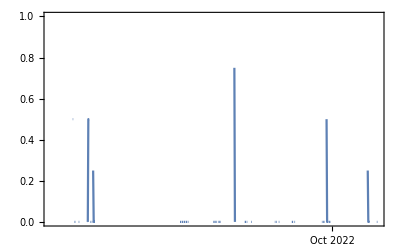

```mathematica
DateListPlot[%117]
```

```mathematica
MoonPosition[]
```

{192.41 °,26.82 °}

```mathematica
MoonPosition[CelestialSystem->"Horizon"]
```

{340.8 °,-72. °}

```mathematica
MoonPosition[CelestialSystem->"Equatorial"]
```

{21.345 ^h,-21.238 °}

```mathematica
MoonPosition[]
```

{340.93 °,-72.01 °}

```mathematica
{MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]}
```

{{21.346 ^h,-21.235 °},{21.346 ^h,-21.235 °}}

```mathematica
{MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]}
```

{{341.66 °,-72.07 °},{341.66 °,-72.08 °}}

Fri 2 Sep 2022

```mathematica
FlightData[Entity["Airport","KMSP"]->Entity["Airport","KSNA"],"Flights",DateObject[{2022,9,2},"Day"]]
```

{Delta Air Lines flight 2775 (departing 1 Sep 2022,4:58 pm CDT)}

```mathematica
GeoNearest["Building",GeoNearest["WeatherStation",Here]]
```

{{West Virginia State Capitol}}

```mathematica
GeoGraphics[GeoNearest["WeatherStation",Here],GeoRange->Quantity[10, "Kilometers"]]
```

-Graphics-

```mathematica
FlightData[Entity["Airport","KMSP"]->Entity["Airport","KLAX"],"Flights",DateObject[{2022,9,2},"Day"]]
```

{Delta Air Lines flight 2101 (departing 1 Sep 2022,7:11 am CDT),Delta Air Lines flight 2163 (departing 1 Sep 2022,9:33 am CDT),Delta Air Lines flight 2089 (departing 1 Sep 2022,11:29 am CDT),Sun Country Airlines flight 427 (departing 1 Sep 2022,12:34 pm CDT),Delta Air Lines flight 1177 (departing 1 Sep 2022,1:03 pm CDT),Delta Air Lines flight 920 (departing 1 Sep 2022,2:57 pm CDT),Delta Air Lines flight 1632 (departing 1 Sep 2022,9:58 pm CDT)}

```mathematica
TimeZoneConvert[DateObject[{2022,9,1,13,38,0.},"Instant","Gregorian",-4.],Entity["TimeZone","America/Chicago"]]
```

Thu 1 Sep 2022 12:38:00CDT

```mathematica
TimeObject[DateObject[{2022,9,1,12,38,0.},"Instant","Gregorian","America/Chicago"]]
```

12:38:00CDTTimeObject[{12,38,0.},Instant,America/Chicago]

```mathematica
Entity["Flight","202209010000235186"]["PropertyAssociation"]
```

<|flight ID→SCX427,aircraft type→Boeing 737 MAX 8,airline→Sun Country Airlines d/b/a Mn Airlines,arrival airport→Los Angeles International Airport,arrival delay time→1. min,landing time→Thu 1 Sep 2022 16:47:00GMT-4,departure airport→Minneapolis-St. Paul International Airport,departure delay time→-4. min,takeoff time→Thu 1 Sep 2022 13:34:00GMT-4,distance traveled→2501.85 km,entity classes→Missing[NotAvailable],flight duration→3 10.,flight map→GeoGraphics[{RGBColor[1, 0, 0],Thickness[Large],Arrow[GeoPosition[…]]}],flight number→427,flight status→landed,future flights→{Sun Country Airlines flight 427 (departing 1 Sep 2022,12:34 pm CDT),Sun Country Airlines flight 427 (departing 4 Sep 2022,12:08 pm CDT),Sun Country Airlines flight 427 (departing 6 Sep 2022,12:36 pm CDT),Sun Country Airlines flight 427 (departing 6 Sep 2022,12:37 pm CDT),Sun Country Airlines flight 427 (departing 8 Sep 2022,8:38 am CDT)},landed→True,maximum altitude→10972.8 m,maximum ground speed→880. km/h,mean cruising ground speed→840. km/h,mean ground speed→790. km/h,name→Sun Country Airlines flight 427 (departing 1 Sep 2022,12:34 pm CDT),scheduled landing time→Thu 1 Sep 2022 16:45:38GMT-4,scheduled takeoff time→Thu 1 Sep 2022 13:38:00GMT-4,past flights→{Sun Country Airlines flight 427 (departing 1 Sep 2022,12:34 pm CDT),Sun Country Airlines flight 427 (departing 28 Aug 2022,12:02 pm CDT),Sun Country Airlines flight 427 (departing 26 Aug 2022,12:10 pm CDT),Sun Country Airlines flight 427 (departing 26 Aug 2022,12:07 pm CDT),Sun Country Airlines flight 427 (departing 23 Aug 2022,1:08 pm CDT)},altitude→TimeSeries[…],flight path→TimeSeries[…],direction heading→TimeSeries[…],rate of climb→TimeSeries[…],ground speed→TimeSeries[…],time since take off→Missing[NotInFlight]|>

```mathematica
Select[GeoDistance[#,]<&][Union[Values[%214]]]
```

{Los Angeles International Airport,John Wayne Airport}

```mathematica
Union[Values[%214]]
```

{Keflavík International Airport,Pierre Elliott Trudeau International,Winnipeg International Airport,Calgary International Airport,Toronto Pearson International Airport,London Heathrow Airport,Amsterdam Airport Schiphol,Aberdeen Regional Airport,Fort Worth Alliance Airport,Hartsfield-Jackson Atlanta International Airport,Outagamie County Regional Airport,Austin-Bergstrom International Airport,Asheville Regional Airport,Chandler Field Airport,Bradley International Airport,King County International Airport,Billings Logan International Airport,Bismarck Municipal Airport,Bemidji Regional Airport,Nashville International Airport,Boise Airport,Logan Airport,Brainerd Lakes Regional Airport,Burlington International Airport,Baltimore/Washington International Thurgood Marshall Airport,Gallatin Field Airport,Charleston International Airport,The Eastern Iowa Airport,Chippewa County International Airport,Cleveland-Hopkins Airport,Charlotte/Douglas International Airport,Port Columbus International Airport,Cincinnati/Northern Kentucky International Airport,Central Wisconsin Airport,Reagan Washington National Airport,Denver International Airport,Dallas-Fort Worth International Airport,Duluth International Airport,Des Moines International Airport,Detroit Metropolitan Wayne County Airport,Eveleth-Virginia Municipal Airport,Newark Liberty International Airport,Hector International Airport,Joe Foss Field Airport,Spokane International Airport,Grand Rapids/Itasca County Airport,Straubel International Airport,Gerald Ford Airport,Chisholm-Hibbing Airport,Houston Hobby Airport,Washington Dulles International Airport,Bush Intercontinental Airport,Wichita Mid-Continent Airport,Airborne Airpark,Ford Airport,Indianapolis International Airport,Falls International Airport,Gogebic-Iron County Airport,John F. Kennedy International Airport,John C. Tune Airport,Lakeland Linder Regional Airport,McCarran International Airport,Los Angeles International Airport,LaGuardia Airport,Lincoln Airport,La Crosse Municipal Airport,Kansas City Airport,Orlando International Airport,Midway Airport,Memphis International Airport,Mitchell International Airport,Quad City Airport,Minot International Airport,Dane County Regional Airport,New Orleans International Airport,Will Rogers World Airport,Omaha Eppley Airport,Quonset State Airport,Chicago O'Hare International Airport,Portland International Airport,Philadelphia International Airport,Phoenix Sky Harbor International Airport,Pittsburgh International Airport,Tri-Cities Airport,Rapid City Regional Airport,Raleigh-Durham International Airport,Rockford International Airport,Rhinelander-Oneida County Airport,Reno/Tahoe International Airport,Rice Lake Regional Airport,Rochester International Airport,Southwest Florida International Airport,San Diego International Airport,San Antonio Airport,Savannah International Airport,South Bend Regional Airport,Louisville International Airport,Seattle-Tacoma International Airport,San Francisco International Airport,San Jose Mineta Airport,Salt Lake City International Airport,Sacramento International Airport,John Wayne Airport,Sarasota/Bradenton International Airport,St. Louis International Airport,Tampa International Airport,Cherry Capital Airport,Thief River Falls Regional Airport,McGhee Tyson Airport,Charles de Gaulle International Airport,Mexico City International Airport,Cancun International Airport,Fairbanks International Airport,Ted Stevens Anchorage International Airport,Honolulu International Airport,Guapi Airport,Missing[NotAvailable]}

```mathematica
FlightData[->All,"ArrivalAirport",DateObject[{2022,9,2},"Day"]]
```

<|Delta Air Lines flight 8881 (departing 1 Sep 2022,12:11 am CDT)→Midway Airport,Delta Air Lines flight 8878 (departing 1 Sep 2022,12:33 am CDT)→Logan Airport,Contract Air Cargo flight 69 (departing 1 Sep 2022,4:57 am CDT)→Thief River Falls Regional Airport,Southwest Airlines flight 1926 (departing 1 Sep 2022,5:30 am CDT)→Midway Airport,Delta Air Lines flight 437 (departing 1 Sep 2022,5:40 am CDT)→Hartsfield-Jackson Atlanta International Airport,Southwest Airlines flight 1933 (departing 1 Sep 2022,6:07 am CDT)→St. Louis International Airport,United Airlines flight 2149 (departing 1 Sep 2022,6:09 am CDT)→Denver International Airport,American Airlines flight 894 (departing 1 Sep 2022,6:16 am CDT)→Charlotte/Douglas International Airport,Delta Air Lines flight 1510 (departing 1 Sep 2022,6:24 am CDT)→Detroit Metropolitan Wayne County Airport,American Airlines flight 1077 (departing 1 Sep 2022,6:25 am CDT)→Chicago O'Hare International Airport,Southwest Airlines flight 4082 (departing 1 Sep 2022,6:29 am CDT)→Phoenix Sky Harbor International Airport,United Airlines flight 2639 (departing 1 Sep 2022,6:31 am CDT)→Chicago O'Hare International Airport,Sun Country Airlines flight 341 (departing 1 Sep 2022,6:42 am CDT)→Orlando International Airport,Alaska Airlines flight 1017 (departing 1 Sep 2022,6:43 am CDT)→Seattle-Tacoma International Airport,Southwest Airlines flight 1924 (departing 1 Sep 2022,6:48 am CDT)→Denver International Airport,Air Canada Jazz flight 716 (departing 1 Sep 2022,6:49 am CDT)→Toronto Pearson International Airport,United Airlines flight 2667 (departing 1 Sep 2022,6:50 am CDT)→Newark Liberty International Airport,Sun Country Airlines flight 383 (departing 1 Sep 2022,6:50 am CDT)→Southwest Florida International Airport,UPS Airlines flight 496 (departing 1 Sep 2022,6:57 am CDT)→Winnipeg International Airport,JetBlue Airways flight 418 (departing 1 Sep 2022,6:58 am CDT)→John F. Kennedy International Airport,Delta Air Lines flight 1019 (departing 1 Sep 2022,6:59 am CDT)→Seattle-Tacoma International Airport,American Airlines flight 2111 (departing 1 Sep 2022,7:03 am CDT)→Dallas-Fort Worth International Airport,Mountain Air Cargo flight 8553 (departing 1 Sep 2022,7:04 am CDT)→Duluth International Airport,Delta Air Lines flight 408 (departing 1 Sep 2022,7:05 am CDT)→Hartsfield-Jackson Atlanta International Airport,Sun Country Airlines flight 101 (departing 1 Sep 2022,7:07 am CDT)→McCarran International Airport,Delta Air Lines flight 2101 (departing 1 Sep 2022,7:11 am CDT)→Los Angeles International Airport,Delta Air Lines flight 2168 (departing 1 Sep 2022,7:12 am CDT)→Nashville International Airport,Delta Air Lines flight 938 (departing 1 Sep 2022,7:13 am CDT)→McCarran International Airport,Delta Air Lines flight 909 (departing 1 Sep 2022,7:14 am CDT)→Logan Airport,Delta Air Lines flight 2953 (departing 1 Sep 2022,7:15 am CDT)→Chicago O'Hare International Airport,Delta Air Lines flight 1280 (departing 1 Sep 2022,7:16 am CDT)→Southwest Florida International Airport,Sun Country Airlines flight 233 (departing 1 Sep 2022,7:21 am CDT)→Newark Liberty International Airport,SkyWest Airlines flight 4016 (departing 1 Sep 2022,7:22 am CDT)→Midway Airport,Sun Country Airlines flight 391 (departing 1 Sep 2022,7:22 am CDT)→San Francisco International Airport,Bemidji Airlines flight 62 (departing 1 Sep 2022,7:23 am CDT)→Chandler Field Airport,SkyWest Airlines flight 3789 (departing 1 Sep 2022,7:24 am CDT)→Indianapolis International Airport,Bemidji Airlines flight 70 (departing 1 Sep 2022,7:25 am CDT)→Falls International Airport,Delta Air Lines flight 2199 (departing 1 Sep 2022,7:26 am CDT)→LaGuardia Airport,Bemidji Airlines flight 58 (departing 1 Sep 2022,7:26 am CDT)→Duluth International Airport,tail number EDV4980 (departing 1 Sep 2022,7:27 am CDT)→John F. Kennedy International Airport,Delta Air Lines flight 835 (departing 1 Sep 2022,7:27 am CDT)→Orlando International Airport,Bemidji Airlines flight 48 (departing 1 Sep 2022,7:28 am CDT)→Rice Lake Regional Airport,Southwest Airlines flight 6445 (departing 1 Sep 2022,7:29 am CDT)→Baltimore/Washington International Thurgood Marshall Airport,Sun Country Airlines flight 251 (departing 1 Sep 2022,7:30 am CDT)→Logan Airport,SkyWest Airlines flight 3922 (departing 1 Sep 2022,7:31 am CDT)→Gerald Ford Airport,Bemidji Airlines flight 52 (departing 1 Sep 2022,7:32 am CDT)→Bemidji Regional Airport,SkyWest Airlines flight 4014 (departing 1 Sep 2022,7:33 am CDT)→Port Columbus International Airport,Bemidji Airlines flight 54 (departing 1 Sep 2022,7:33 am CDT)→Eveleth-Virginia Municipal Airport,Delta Air Lines flight 1530 (departing 1 Sep 2022,7:33 am CDT)→Bush Intercontinental Airport,Bemidji Airlines flight 80 (departing 1 Sep 2022,7:34 am CDT)→Grand Rapids/Itasca County Airport,Bemidji Airlines flight 46 (departing 1 Sep 2022,7:34 am CDT)→La Crosse Municipal Airport,Bemidji Airlines flight 72 (departing 1 Sep 2022,7:35 am CDT)→Brainerd Lakes Regional Airport,Sun Country Airlines flight 635 (departing 1 Sep 2022,7:36 am CDT)→Nashville International Airport,Sun Country Airlines flight 269 (departing 1 Sep 2022,7:37 am CDT)→Philadelphia International Airport,SkyWest Airlines flight 3691 (departing 1 Sep 2022,7:39 am CDT)→St. Louis International Airport,tail number EDV4703 (departing 1 Sep 2022,7:40 am CDT)→Cleveland-Hopkins Airport,Southwest Airlines flight 2972 (departing 1 Sep 2022,7:45 am CDT)→Midway Airport,UPS Airlines flight 2557 (departing 1 Sep 2022,7:49 am CDT)→Louisville International Airport,Sun Country Airlines flight 1267 (departing 1 Sep 2022,7:52 am CDT)→Charleston International Airport,American Airlines flight 2985 (departing 1 Sep 2022,7:53 am CDT)→Phoenix Sky Harbor International Airport,UPS Airlines flight 5525 (departing 1 Sep 2022,7:54 am CDT)→Louisville International Airport,Sun Country Airlines flight 193 (departing 1 Sep 2022,7:55 am CDT)→Baltimore/Washington International Thurgood Marshall Airport,Republic Airlines flight 3475 (departing 1 Sep 2022,8:04 am CDT)→Chicago O'Hare International Airport,Sun Country Airlines flight 207 (departing 1 Sep 2022,8:10 am CDT)→Savannah International Airport,FedEx Express flight 645 (departing 1 Sep 2022,8:12 am CDT)→Memphis International Airport,Sun Country Airlines flight 471 (departing 1 Sep 2022,8:14 am CDT)→Ted Stevens Anchorage International Airport,Sun Country Airlines flight 651 (departing 1 Sep 2022,8:28 am CDT)→Denver International Airport,SkyWest Airlines flight 3893 (departing 1 Sep 2022,8:36 am CDT)→Kansas City Airport,Sun Country Airlines flight 1045 (departing 1 Sep 2022,8:38 am CDT)→Burlington International Airport,Southwest Airlines flight 976 (departing 1 Sep 2022,8:42 am CDT)→Austin-Bergstrom International Airport,Delta Air Lines flight 1009 (departing 1 Sep 2022,8:43 am CDT)→Salt Lake City International Airport,Sun Country Airlines flight 367 (departing 1 Sep 2022,8:44 am CDT)→Tampa International Airport,SkyWest Airlines flight 4023 (departing 1 Sep 2022,8:56 am CDT)→Dane County Regional Airport,SkyWest Airlines flight 4327 (departing 1 Sep 2022,8:58 am CDT)→Chisholm-Hibbing Airport,SkyWest Airlines flight 3550 (departing 1 Sep 2022,9:02 am CDT)→Toronto Pearson International Airport,Delta Air Lines flight 2213 (departing 1 Sep 2022,9:03 am CDT)→Detroit Metropolitan Wayne County Airport,Bemidji Airlines flight 1324 (departing 1 Sep 2022,9:04 am CDT)→Thief River Falls Regional Airport,SkyWest Airlines flight 3984 (departing 1 Sep 2022,9:05 am CDT)→Omaha Eppley Airport,Delta Air Lines flight 2439 (departing 1 Sep 2022,9:07 am CDT)→Austin-Bergstrom International Airport,SkyWest Airlines flight 4327 (departing 1 Sep 2022,9:08 am CDT)→Chisholm-Hibbing Airport,SkyWest Airlines flight 4023 (departing 1 Sep 2022,9:08 am CDT)→Dane County Regional Airport,Southwest Airlines flight 598 (departing 1 Sep 2022,9:10 am CDT)→Denver International Airport,SkyWest Airlines flight 104 (departing 1 Sep 2022,9:10 am CDT)→Hector International Airport,tail number EDV4652 (departing 1 Sep 2022,9:10 am CDT)→Cincinnati/Northern Kentucky International Airport,PSA Airlines flight 5182 (departing 1 Sep 2022,9:12 am CDT)→Reagan Washington National Airport,SkyWest Airlines flight 4118 (departing 1 Sep 2022,9:13 am CDT)→Pittsburgh International Airport,SkyWest Airlines flight 106 (departing 1 Sep 2022,9:14 am CDT)→Mitchell International Airport,Delta Air Lines flight 867 (departing 1 Sep 2022,9:15 am CDT)→Seattle-Tacoma International Airport,Delta Air Lines flight 1881 (departing 1 Sep 2022,9:16 am CDT)→Cancun International Airport,Delta Air Lines flight 375 (departing 1 Sep 2022,9:16 am CDT)→Hartsfield-Jackson Atlanta International Airport,tail number EDV5468 (departing 1 Sep 2022,9:17 am CDT)→Joe Foss Field Airport,Delta Air Lines flight 2658 (departing 1 Sep 2022,9:18 am CDT)→San Antonio Airport,SkyWest Airlines flight 125 (departing 1 Sep 2022,9:20 am CDT)→Memphis International Airport,Southwest Airlines flight 976 (departing 1 Sep 2022,9:21 am CDT)→Austin-Bergstrom International Airport,FedEx Express flight 420 (departing 1 Sep 2022,9:22 am CDT)→Memphis International Airport,Delta Air Lines flight 611 (departing 1 Sep 2022,9:23 am CDT)→Mexico City International Airport,SkyWest Airlines flight 3905 (departing 1 Sep 2022,9:30 am CDT)→Washington Dulles International Airport,tail number EDV4652 (departing 1 Sep 2022,9:31 am CDT)→Cincinnati/Northern Kentucky International Airport,Delta Air Lines flight 2163 (departing 1 Sep 2022,9:33 am CDT)→Los Angeles International Airport,Sun Country Airlines flight 631 (departing 1 Sep 2022,9:35 am CDT)→Nashville International Airport,Delta Air Lines flight 2881 (departing 1 Sep 2022,9:39 am CDT)→Phoenix Sky Harbor International Airport,United Airlines flight 2490 (departing 1 Sep 2022,9:41 am CDT)→Denver International Airport,Delta Air Lines flight 2845 (departing 1 Sep 2022,9:46 am CDT)→San Diego International Airport,Sun Country Airlines flight 681 (departing 1 Sep 2022,9:51 am CDT)→Bush Intercontinental Airport,Key Lime Air flight 5110 (departing 1 Sep 2022,9:57 am CDT)→Thief River Falls Regional Airport,Delta Air Lines flight 2452 (departing 1 Sep 2022,10:04 am CDT)→Hartsfield-Jackson Atlanta International Airport,Mesa Airlines flight 1185 (departing 1 Sep 2022,10:05 am CDT)→Cincinnati/Northern Kentucky International Airport,Delta Air Lines flight 1233 (departing 1 Sep 2022,10:07 am CDT)→Chicago O'Hare International Airport,SkyWest Airlines flight 123 (departing 1 Sep 2022,10:07 am CDT)→Rochester International Airport,SkyWest Airlines flight 3896 (departing 1 Sep 2022,10:12 am CDT)→Outagamie County Regional Airport,SkyWest Airlines flight 138 (departing 1 Sep 2022,10:14 am CDT)→Rapid City Regional Airport,Delta Air Lines flight 900 (departing 1 Sep 2022,10:16 am CDT)→LaGuardia Airport,SkyWest Airlines flight 3840 (departing 1 Sep 2022,10:17 am CDT)→Bush Intercontinental Airport,tail number NCJ70-1 (departing 1 Sep 2022,10:18 am CDT)→Port Columbus International Airport,Delta Air Lines flight 737 (departing 1 Sep 2022,10:21 am CDT)→Logan Airport,United Airlines flight 1710 (departing 1 Sep 2022,10:21 am CDT)→Chicago O'Hare International Airport,SkyWest Airlines flight 4260 (departing 1 Sep 2022,10:22 am CDT)→Missing[NotAvailable],SkyWest Airlines flight 115 (departing 1 Sep 2022,10:29 am CDT)→Wichita Mid-Continent Airport,SkyWest Airlines flight 138 (departing 1 Sep 2022,10:34 am CDT)→Rapid City Regional Airport,tail number GAJ510 (departing 1 Sep 2022,10:37 am CDT)→John C. Tune Airport,tail number NCJ50-1 (departing 1 Sep 2022,10:42 am CDT)→Joe Foss Field Airport,Southwest Airlines flight 2123 (departing 1 Sep 2022,10:43 am CDT)→Midway Airport,tail number EDV4854 (departing 1 Sep 2022,10:44 am CDT)→Des Moines International Airport,NetJets flight 591 (departing 1 Sep 2022,10:47 am CDT)→Quonset State Airport,SkyWest Airlines flight 3643 (departing 1 Sep 2022,10:47 am CDT)→Minot International Airport,tail number EDV4854 (departing 1 Sep 2022,10:54 am CDT)→Des Moines International Airport,SkyWest Airlines flight 3643 (departing 1 Sep 2022,10:56 am CDT)→Minot International Airport,Delta Air Lines flight 1330 (departing 1 Sep 2022,10:57 am CDT)→Dallas-Fort Worth International Airport,tail number NKS169-1 (departing 1 Sep 2022,10:57 am CDT)→McCarran International Airport,tail number NKS169-1 (departing 1 Sep 2022,10:59 am CDT)→McCarran International Airport,SkyWest Airlines flight 3920 (departing 1 Sep 2022,11:02 am CDT)→Bismarck Municipal Airport,Sun Country Airlines flight 111 (departing 1 Sep 2022,11:02 am CDT)→McCarran International Airport,Delta Air Lines flight 1015 (departing 1 Sep 2022,11:07 am CDT)→Salt Lake City International Airport,Southwest Airlines flight 105 (departing 1 Sep 2022,11:12 am CDT)→Denver International Airport,Delta Air Lines flight 894 (departing 1 Sep 2022,11:13 am CDT)→Seattle-Tacoma International Airport,tail number EDV4917 (departing 1 Sep 2022,11:14 am CDT)→John F. Kennedy International Airport,Delta Air Lines flight 2365 (departing 1 Sep 2022,11:16 am CDT)→San Francisco International Airport,SkyWest Airlines flight 3670 (departing 1 Sep 2022,11:16 am CDT)→Omaha Eppley Airport,JetBlue Airways flight 1236 (departing 1 Sep 2022,11:26 am CDT)→Logan Airport,Delta Air Lines flight 2089 (departing 1 Sep 2022,11:29 am CDT)→Los Angeles International Airport,Republic Airlines flight 4798 (departing 1 Sep 2022,11:32 am CDT)→LaGuardia Airport,Delta Air Lines flight 1465 (departing 1 Sep 2022,11:33 am CDT)→San Diego International Airport,United Airlines flight 725 (departing 1 Sep 2022,11:35 am CDT)→Chicago O'Hare International Airport,Allegiant Air flight 1399 (departing 1 Sep 2022,11:39 am CDT)→McGhee Tyson Airport,SkyWest Airlines flight 3751 (departing 1 Sep 2022,11:40 am CDT)→Hector International Airport,SkyWest Airlines flight 128 (departing 1 Sep 2022,11:44 am CDT)→Falls International Airport,American Airlines flight 2593 (departing 1 Sep 2022,11:56 am CDT)→Dallas-Fort Worth International Airport,Delta Air Lines flight 887 (departing 1 Sep 2022,11:56 am CDT)→Sacramento International Airport,SkyWest Airlines flight 175 (departing 1 Sep 2022,12:05 pm CDT)→Midway Airport,Delta Air Lines flight 2125 (departing 1 Sep 2022,12:10 pm CDT)→Dallas-Fort Worth International Airport,Sun Country Airlines flight 427 (departing 1 Sep 2022,12:34 pm CDT)→Los Angeles International Airport,Mesa Airlines flight 6020 (departing 1 Sep 2022,12:35 pm CDT)→Washington Dulles International Airport,PSA Airlines flight 5182 (departing 1 Sep 2022,12:39 pm CDT)→Reagan Washington National Airport,tail number ENY3988 (departing 1 Sep 2022,12:39 pm CDT)→Chicago O'Hare International Airport,Delta Air Lines flight 435 (departing 1 Sep 2022,12:45 pm CDT)→Honolulu International Airport,Delta Air Lines flight 922 (departing 1 Sep 2022,12:52 pm CDT)→Detroit Metropolitan Wayne County Airport,SkyWest Airlines flight 3705 (departing 1 Sep 2022,12:53 pm CDT)→Cleveland-Hopkins Airport,SkyWest Airlines flight 3766 (departing 1 Sep 2022,12:56 pm CDT)→Kansas City Airport,tail number EDV4985 (departing 1 Sep 2022,12:58 pm CDT)→The Eastern Iowa Airport,SkyWest Airlines flight 199 (departing 1 Sep 2022,1:01 pm CDT)→Chippewa County International Airport,SkyWest Airlines flight 3579 (departing 1 Sep 2022,1:02 pm CDT)→Indianapolis International Airport,Delta Air Lines flight 1177 (departing 1 Sep 2022,1:03 pm CDT)→Los Angeles International Airport,SkyWest Airlines flight 4242 (departing 1 Sep 2022,1:05 pm CDT)→Brainerd Lakes Regional Airport,tail number EDV4720 (departing 1 Sep 2022,1:07 pm CDT)→Central Wisconsin Airport,SkyWest Airlines flight 4109 (departing 1 Sep 2022,1:07 pm CDT)→Dane County Regional Airport,SkyWest Airlines flight 171 (departing 1 Sep 2022,1:08 pm CDT)→St. Louis International Airport,tail number EDV5233 (departing 1 Sep 2022,1:09 pm CDT)→Cincinnati/Northern Kentucky International Airport,Delta Air Lines flight 2057 (departing 1 Sep 2022,1:11 pm CDT)→Raleigh-Durham International Airport,SkyWest Airlines flight 4094 (departing 1 Sep 2022,1:12 pm CDT)→Duluth International Airport,SkyWest Airlines flight 3845 (departing 1 Sep 2022,1:12 pm CDT)→Gerald Ford Airport,SkyWest Airlines flight 4026 (departing 1 Sep 2022,1:18 pm CDT)→La Crosse Municipal Airport,SkyWest Airlines flight 3920 (departing 1 Sep 2022,1:20 pm CDT)→Bismarck Municipal Airport,Delta Air Lines flight 1589 (departing 1 Sep 2022,1:20 pm CDT)→Chicago O'Hare International Airport,Delta Air Lines flight 434 (departing 1 Sep 2022,1:22 pm CDT)→Hartsfield-Jackson Atlanta International Airport,SkyWest Airlines flight 4097 (departing 1 Sep 2022,1:23 pm CDT)→Joe Foss Field Airport,Catex, Compagnie flight 868 (departing 1 Sep 2022,1:24 pm CDT)→Austin-Bergstrom International Airport,Key Lime Air flight 5111 (departing 1 Sep 2022,1:27 pm CDT)→Gogebic-Iron County Airport,SkyWest Airlines flight 3751 (departing 1 Sep 2022,1:29 pm CDT)→Hector International Airport,SkyWest Airlines flight 3903 (departing 1 Sep 2022,1:33 pm CDT)→Port Columbus International Airport,Air Canada Jazz flight 768 (departing 1 Sep 2022,1:36 pm CDT)→Pierre Elliott Trudeau International,Delta Air Lines flight 1020 (departing 1 Sep 2022,1:38 pm CDT)→LaGuardia Airport,SkyWest Airlines flight 3562 (departing 1 Sep 2022,1:43 pm CDT)→Newark Liberty International Airport,SkyWest Airlines flight 3705 (departing 1 Sep 2022,1:50 pm CDT)→Cleveland-Hopkins Airport,American Airlines flight 2084 (departing 1 Sep 2022,1:55 pm CDT)→Charlotte/Douglas International Airport,Sun Country Airlines flight 3034 (departing 1 Sep 2022,2:10 pm CDT)→Lakeland Linder Regional Airport,SkyWest Airlines flight 3872 (departing 1 Sep 2022,2:12 pm CDT)→Louisville International Airport,SkyWest Airlines flight 3519 (departing 1 Sep 2022,2:12 pm CDT)→Mitchell International Airport,Southwest Airlines flight 256 (departing 1 Sep 2022,2:16 pm CDT)→Midway Airport,tail number EDV5462 (departing 1 Sep 2022,2:25 pm CDT)→Cherry Capital Airport,Sun Country Airlines flight 661 (departing 1 Sep 2022,2:33 pm CDT)→New Orleans International Airport,Delta Air Lines flight 1488 (departing 1 Sep 2022,2:34 pm CDT)→Charlotte/Douglas International Airport,tail number EDV4940 (departing 1 Sep 2022,2:35 pm CDT)→Quad City Airport,tail number EDV4649 (departing 1 Sep 2022,2:40 pm CDT)→John F. Kennedy International Airport,United Airlines flight 1575 (departing 1 Sep 2022,2:42 pm CDT)→Newark Liberty International Airport,Delta Air Lines flight 2699 (departing 1 Sep 2022,2:43 pm CDT)→Austin-Bergstrom International Airport,Alaska Airlines flight 1338 (departing 1 Sep 2022,2:47 pm CDT)→Seattle-Tacoma International Airport,SkyWest Airlines flight 3947 (departing 1 Sep 2022,2:51 pm CDT)→Will Rogers World Airport,Southwest Airlines flight 2824 (departing 1 Sep 2022,2:52 pm CDT)→Denver International Airport,Sun Country Airlines flight 8292 (departing 1 Sep 2022,2:53 pm CDT)→Central Wisconsin Airport,Sun Country Airlines flight 395 (departing 1 Sep 2022,2:54 pm CDT)→San Francisco International Airport,Delta Air Lines flight 920 (departing 1 Sep 2022,2:57 pm CDT)→Los Angeles International Airport,Sun Country Airlines flight 657 (departing 1 Sep 2022,2:58 pm CDT)→Denver International Airport,SkyWest Airlines flight 140 (departing 1 Sep 2022,2:58 pm CDT)→Rapid City Regional Airport,Sun Country Airlines flight 395 (departing 1 Sep 2022,3:03 pm CDT)→San Francisco International Airport,Delta Air Lines flight 993 (departing 1 Sep 2022,3:10 pm CDT)→Salt Lake City International Airport,Sun Country Airlines flight 285 (departing 1 Sep 2022,3:15 pm CDT)→Seattle-Tacoma International Airport,Sun Country Airlines flight 295 (departing 1 Sep 2022,3:22 pm CDT)→Portland International Airport,Sun Country Airlines flight 295 (departing 1 Sep 2022,3:23 pm CDT)→Portland International Airport,Delta Air Lines flight 832 (departing 1 Sep 2022,3:24 pm CDT)→Logan Airport,SkyWest Airlines flight 3803 (departing 1 Sep 2022,3:27 pm CDT)→Memphis International Airport,NetJets flight 900 (departing 1 Sep 2022,3:28 pm CDT)→Houston Hobby Airport,Delta Air Lines flight 2154 (departing 1 Sep 2022,3:30 pm CDT)→Denver International Airport,Sun Country Airlines flight 407 (departing 1 Sep 2022,3:31 pm CDT)→San Diego International Airport,SkyWest Airlines flight 4236 (departing 1 Sep 2022,3:32 pm CDT)→Ford Airport,SkyWest Airlines flight 112 (departing 1 Sep 2022,3:35 pm CDT)→Pittsburgh International Airport,SkyWest Airlines flight 3631 (departing 1 Sep 2022,3:40 pm CDT)→Omaha Eppley Airport,SkyWest Airlines flight 3710 (departing 1 Sep 2022,3:42 pm CDT)→St. Louis International Airport,SkyWest Airlines flight 4102 (departing 1 Sep 2022,3:48 pm CDT)→Joe Foss Field Airport,Delta Air Lines flight 2664 (departing 1 Sep 2022,3:54 pm CDT)→Gerald Ford Airport,Delta Air Lines flight 2555 (departing 1 Sep 2022,3:56 pm CDT)→Detroit Metropolitan Wayne County Airport,Mesa Airlines flight 6017 (departing 1 Sep 2022,4:00 pm CDT)→Bush Intercontinental Airport,Bombardier Aerospace flight 453 (departing 1 Sep 2022,4:02 pm CDT)→Mitchell International Airport,Delta Air Lines flight 879 (departing 1 Sep 2022,4:05 pm CDT)→McCarran International Airport,Delta Air Lines flight 513 (departing 1 Sep 2022,4:05 pm CDT)→Guapi Airport,Sun Country Airlines flight 625 (departing 1 Sep 2022,4:07 pm CDT)→San Antonio Airport,SkyWest Airlines flight 122 (departing 1 Sep 2022,4:08 pm CDT)→Falls International Airport,tail number EDV4888 (departing 1 Sep 2022,4:08 pm CDT)→Cincinnati/Northern Kentucky International Airport,NetJets flight 216 (departing 1 Sep 2022,4:09 pm CDT)→King County International Airport,Sun Country Airlines flight 261 (departing 1 Sep 2022,4:11 pm CDT)→Chicago O'Hare International Airport,SkyWest Airlines flight 151 (departing 1 Sep 2022,4:12 pm CDT)→Bemidji Regional Airport,Air Canada Jazz flight 722 (departing 1 Sep 2022,4:23 pm CDT)→Toronto Pearson International Airport,American Airlines flight 2203 (departing 1 Sep 2022,4:23 pm CDT)→Dallas-Fort Worth International Airport,SkyWest Airlines flight 3856 (departing 1 Sep 2022,4:29 pm CDT)→Duluth International Airport,Republic Airlines flight 4523 (departing 1 Sep 2022,4:31 pm CDT)→LaGuardia Airport,Sun Country Airlines flight 215 (departing 1 Sep 2022,4:33 pm CDT)→Asheville Regional Airport,Delta Air Lines flight 1675 (departing 1 Sep 2022,4:36 pm CDT)→Bush Intercontinental Airport,Delta Air Lines flight 198 (departing 1 Sep 2022,4:36 pm CDT)→Charles de Gaulle International Airport,SkyWest Airlines flight 3994 (departing 1 Sep 2022,4:41 pm CDT)→Midway Airport,Sun Country Airlines flight 219 (departing 1 Sep 2022,4:45 pm CDT)→Cincinnati/Northern Kentucky International Airport,Delta Air Lines flight 426 (departing 1 Sep 2022,4:46 pm CDT)→Hartsfield-Jackson Atlanta International Airport,SkyWest Airlines flight 4054 (departing 1 Sep 2022,4:49 pm CDT)→Rochester International Airport,Sun Country Airlines flight 633 (departing 1 Sep 2022,4:51 pm CDT)→Nashville International Airport,Delta Air Lines flight 2946 (departing 1 Sep 2022,4:55 pm CDT)→Dallas-Fort Worth International Airport,Air Transport International flight 3495 (departing 1 Sep 2022,4:56 pm CDT)→Airborne Airpark,United Airlines flight 2272 (departing 1 Sep 2022,4:58 pm CDT)→Denver International Airport,Delta Air Lines flight 2775 (departing 1 Sep 2022,4:58 pm CDT)→John Wayne Airport,Delta Air Lines flight 2202 (departing 1 Sep 2022,4:59 pm CDT)→Raleigh-Durham International Airport,Bemidji Airlines flight 1323 (departing 1 Sep 2022,5:00 pm CDT)→Thief River Falls Regional Airport,Southwest Airlines flight 1833 (departing 1 Sep 2022,5:02 pm CDT)→Baltimore/Washington International Thurgood Marshall Airport,Delta Air Lines flight 160 (departing 1 Sep 2022,5:04 pm CDT)→Amsterdam Airport Schiphol,Delta Air Lines flight 160 (departing 1 Sep 2022,5:06 pm CDT)→Amsterdam Airport Schiphol,SkyWest Airlines flight 4267 (departing 1 Sep 2022,5:07 pm CDT)→Rhinelander-Oneida County Airport,Sun Country Airlines flight 1273 (departing 1 Sep 2022,5:07 pm CDT)→Reno/Tahoe International Airport,Delta Air Lines flight 2157 (departing 1 Sep 2022,5:11 pm CDT)→Sarasota/Bradenton International Airport,SkyWest Airlines flight 4627 (departing 1 Sep 2022,5:22 pm CDT)→Midway Airport,Sun Country Airlines flight 107 (departing 1 Sep 2022,5:29 pm CDT)→McCarran International Airport,Delta Air Lines flight 10 (departing 1 Sep 2022,5:35 pm CDT)→London Heathrow Airport,Key Lime Air flight 5120 (departing 1 Sep 2022,5:37 pm CDT)→Thief River Falls Regional Airport,SkyWest Airlines flight 4070 (departing 1 Sep 2022,5:39 pm CDT)→Dane County Regional Airport,Delta Air Lines flight 10 (departing 1 Sep 2022,5:41 pm CDT)→London Heathrow Airport,SkyWest Airlines flight 4070 (departing 1 Sep 2022,5:44 pm CDT)→Dane County Regional Airport,Sun Country Airlines flight 501 (departing 1 Sep 2022,5:45 pm CDT)→Dallas-Fort Worth International Airport,SkyWest Airlines flight 4032 (departing 1 Sep 2022,5:46 pm CDT)→Outagamie County Regional Airport,tail number ENY3328 (departing 1 Sep 2022,5:51 pm CDT)→Reagan Washington National Airport,tail number ENY3948 (departing 1 Sep 2022,5:53 pm CDT)→Chicago O'Hare International Airport,American Airlines flight 2885 (departing 1 Sep 2022,5:53 pm CDT)→Charlotte/Douglas International Airport,SkyWest Airlines flight 4460 (departing 1 Sep 2022,5:57 pm CDT)→Mitchell International Airport,Delta Air Lines flight 719 (departing 1 Sep 2022,5:59 pm CDT)→San Francisco International Airport,Delta Air Lines flight 719 (departing 1 Sep 2022,6:01 pm CDT)→San Francisco International Airport,Delta Air Lines flight 1411 (departing 1 Sep 2022,6:02 pm CDT)→Tri-Cities Airport,SkyWest Airlines flight 4257 (departing 1 Sep 2022,6:03 pm CDT)→Chisholm-Hibbing Airport,Delta Air Lines flight 423 (departing 1 Sep 2022,6:04 pm CDT)→Hartsfield-Jackson Atlanta International Airport,Delta Air Lines flight 2410 (departing 1 Sep 2022,6:11 pm CDT)→Detroit Metropolitan Wayne County Airport,Delta Air Lines flight 2803 (departing 1 Sep 2022,6:17 pm CDT)→San Jose Mineta Airport,Delta Air Lines flight 915 (departing 1 Sep 2022,6:18 pm CDT)→Seattle-Tacoma International Airport,SkyWest Airlines flight 4460 (departing 1 Sep 2022,6:19 pm CDT)→Mitchell International Airport,Republic Airlines flight 3717 (departing 1 Sep 2022,6:19 pm CDT)→Newark Liberty International Airport,Delta Air Lines flight 2410 (departing 1 Sep 2022,6:21 pm CDT)→Detroit Metropolitan Wayne County Airport,Delta Air Lines flight 915 (departing 1 Sep 2022,6:22 pm CDT)→Seattle-Tacoma International Airport,Delta Air Lines flight 701 (departing 1 Sep 2022,6:26 pm CDT)→Fairbanks International Airport,Delta Air Lines flight 2393 (departing 1 Sep 2022,6:30 pm CDT)→Indianapolis International Airport,Delta Air Lines flight 765 (departing 1 Sep 2022,6:30 pm CDT)→Salt Lake City International Airport,Delta Air Lines flight 2978 (departing 1 Sep 2022,6:32 pm CDT)→Calgary International Airport,American Airlines flight 2406 (departing 1 Sep 2022,6:54 pm CDT)→Dallas-Fort Worth International Airport,Delta Air Lines flight 907 (departing 1 Sep 2022,7:29 pm CDT)→Hartsfield-Jackson Atlanta International Airport,Delta Air Lines flight 162 (departing 1 Sep 2022,7:36 pm CDT)→Amsterdam Airport Schiphol,SkyWest Airlines flight 3624 (departing 1 Sep 2022,7:44 pm CDT)→South Bend Regional Airport,tail number NJM455-1 (departing 1 Sep 2022,7:44 pm CDT)→Dane County Regional Airport,Icelandair flight 656 (departing 1 Sep 2022,7:46 pm CDT)→Keflavík International Airport,Delta Air Lines flight 1027 (departing 1 Sep 2022,8:05 pm CDT)→LaGuardia Airport,SkyWest Airlines flight 3602 (departing 1 Sep 2022,8:06 pm CDT)→Washington Dulles International Airport,Delta Air Lines flight 771 (departing 1 Sep 2022,8:08 pm CDT)→Logan Airport,Delta Air Lines flight 2097 (departing 1 Sep 2022,8:09 pm CDT)→Dallas-Fort Worth International Airport,Delta Air Lines flight 1606 (departing 1 Sep 2022,8:11 pm CDT)→Nashville International Airport,SkyWest Airlines flight 3657 (departing 1 Sep 2022,8:12 pm CDT)→La Crosse Municipal Airport,tail number EDV5331 (departing 1 Sep 2022,8:14 pm CDT)→Cincinnati/Northern Kentucky International Airport,Delta Air Lines flight 387 (departing 1 Sep 2022,8:16 pm CDT)→Raleigh-Durham International Airport,SkyWest Airlines flight 4153 (departing 1 Sep 2022,8:17 pm CDT)→Louisville International Airport,Alaska Airlines flight 704 (departing 1 Sep 2022,8:17 pm CDT)→Seattle-Tacoma International Airport,Frontier Airlines flight 461 (departing 1 Sep 2022,8:18 pm CDT)→Denver International Airport,SkyWest Airlines flight 3797 (departing 1 Sep 2022,8:19 pm CDT)→Cleveland-Hopkins Airport,tail number EDV5262 (departing 1 Sep 2022,8:20 pm CDT)→Des Moines International Airport,SkyWest Airlines flight 3509 (departing 1 Sep 2022,8:22 pm CDT)→Mitchell International Airport,SkyWest Airlines flight 4124 (departing 1 Sep 2022,8:23 pm CDT)→Pittsburgh International Airport,tail number DPJ525 (departing 1 Sep 2022,8:25 pm CDT)→Lincoln Airport,SkyWest Airlines flight 3995 (departing 1 Sep 2022,8:26 pm CDT)→Outagamie County Regional Airport,tail number N441CT-1 (departing 1 Sep 2022,8:32 pm CDT)→Aberdeen Regional Airport,tail number EDV4679 (departing 1 Sep 2022,8:35 pm CDT)→Pierre Elliott Trudeau International,SkyWest Airlines flight 3885 (departing 1 Sep 2022,8:36 pm CDT)→Port Columbus International Airport,Delta Air Lines flight 2536 (departing 1 Sep 2022,8:38 pm CDT)→Philadelphia International Airport,Delta Air Lines flight 220 (departing 1 Sep 2022,8:38 pm CDT)→Charles de Gaulle International Airport,Delta Air Lines flight 2149 (departing 1 Sep 2022,8:39 pm CDT)→Bradley International Airport,SkyWest Airlines flight 3923 (departing 1 Sep 2022,8:41 pm CDT)→Indianapolis International Airport,Delta Air Lines flight 2552 (departing 1 Sep 2022,8:42 pm CDT)→Tampa International Airport,Southwest Airlines flight 857 (departing 1 Sep 2022,8:43 pm CDT)→Midway Airport,SkyWest Airlines flight 3615 (departing 1 Sep 2022,8:43 pm CDT)→Toronto Pearson International Airport,Delta Air Lines flight 1192 (departing 1 Sep 2022,8:46 pm CDT)→Orlando International Airport,tail number EDV5287 (departing 1 Sep 2022,8:49 pm CDT)→Cherry Capital Airport,Sun Country Airlines flight 397 (departing 1 Sep 2022,8:52 pm CDT)→San Francisco International Airport,Southwest Airlines flight 1003 (departing 1 Sep 2022,8:57 pm CDT)→Denver International Airport,Delta Air Lines flight 1366 (departing 1 Sep 2022,9:05 pm CDT)→Baltimore/Washington International Thurgood Marshall Airport,Delta Air Lines flight 968 (departing 1 Sep 2022,9:12 pm CDT)→San Francisco International Airport,Delta Air Lines flight 2490 (departing 1 Sep 2022,9:18 pm CDT)→Portland International Airport,SkyWest Airlines flight 108 (departing 1 Sep 2022,9:20 pm CDT)→Missing[NotAvailable],Delta Air Lines flight 1093 (departing 1 Sep 2022,9:21 pm CDT)→Ted Stevens Anchorage International Airport,UPS Airlines flight 561 (departing 1 Sep 2022,9:22 pm CDT)→Dallas-Fort Worth International Airport,FedEx Express flight 1358 (departing 1 Sep 2022,9:26 pm CDT)→Memphis International Airport,Delta Air Lines flight 1149 (departing 1 Sep 2022,9:30 pm CDT)→Seattle-Tacoma International Airport,SkyWest Airlines flight 4266 (departing 1 Sep 2022,9:33 pm CDT)→Bemidji Regional Airport,UPS Airlines flight 557 (departing 1 Sep 2022,9:33 pm CDT)→Philadelphia International Airport,SkyWest Airlines flight 3545 (departing 1 Sep 2022,9:35 pm CDT)→Memphis International Airport,SkyWest Airlines flight 3574 (departing 1 Sep 2022,9:36 pm CDT)→Omaha Eppley Airport,SkyWest Airlines flight 4003 (departing 1 Sep 2022,9:37 pm CDT)→Straubel International Airport,Delta Air Lines flight 1310 (departing 1 Sep 2022,9:38 pm CDT)→Guapi Airport,Delta Air Lines flight 1310 (departing 1 Sep 2022,9:39 pm CDT)→Guapi Airport,Delta Air Lines flight 2922 (departing 1 Sep 2022,9:39 pm CDT)→Dane County Regional Airport,FedEx Express flight 1618 (departing 1 Sep 2022,9:40 pm CDT)→Indianapolis International Airport,SkyWest Airlines flight 4265 (departing 1 Sep 2022,9:43 pm CDT)→Brainerd Lakes Regional Airport,Delta Air Lines flight 2515 (departing 1 Sep 2022,9:43 pm CDT)→San Antonio Airport,UPS Airlines flight 559 (departing 1 Sep 2022,9:47 pm CDT)→Louisville International Airport,FedEx Express flight 1106 (departing 1 Sep 2022,9:47 pm CDT)→Fort Worth Alliance Airport,United Airlines flight 2375 (departing 1 Sep 2022,9:48 pm CDT)→Chicago O'Hare International Airport,Delta Air Lines flight 2527 (departing 1 Sep 2022,9:50 pm CDT)→Kansas City Airport,Delta Air Lines flight 874 (departing 1 Sep 2022,9:51 pm CDT)→Spokane International Airport,Mesa Airlines flight 185 (departing 1 Sep 2022,9:52 pm CDT)→The Eastern Iowa Airport,UPS Airlines flight 555 (departing 1 Sep 2022,9:54 pm CDT)→Rockford International Airport,Delta Air Lines flight 2252 (departing 1 Sep 2022,9:55 pm CDT)→Phoenix Sky Harbor International Airport,Delta Air Lines flight 2915 (departing 1 Sep 2022,9:56 pm CDT)→Gallatin Field Airport,Delta Air Lines flight 1636 (departing 1 Sep 2022,9:57 pm CDT)→St. Louis International Airport,Delta Air Lines flight 1632 (departing 1 Sep 2022,9:58 pm CDT)→Los Angeles International Airport,Delta Air Lines flight 1572 (departing 1 Sep 2022,10:06 pm CDT)→Boise Airport,Delta Air Lines flight 1454 (departing 1 Sep 2022,10:10 pm CDT)→San Diego International Airport,Southwest Airlines flight 874 (departing 1 Sep 2022,10:12 pm CDT)→Midway Airport,Delta Air Lines flight 2877 (departing 1 Sep 2022,10:16 pm CDT)→Billings Logan International Airport,Southwest Airlines flight 874 (departing 1 Sep 2022,10:18 pm CDT)→Midway Airport,SkyWest Airlines flight 4121 (departing 1 Sep 2022,10:56 pm CDT)→Duluth International Airport,SkyWest Airlines flight 3916 (departing 1 Sep 2022,10:57 pm CDT)→Minot International Airport,SkyWest Airlines flight 3827 (departing 1 Sep 2022,11:01 pm CDT)→Rochester International Airport,SkyWest Airlines flight 3603 (departing 1 Sep 2022,11:03 pm CDT)→Bismarck Municipal Airport,SkyWest Airlines flight 3621 (departing 1 Sep 2022,11:05 pm CDT)→Rapid City Regional Airport,Delta Air Lines flight 1730 (departing 1 Sep 2022,11:07 pm CDT)→Hector International Airport,Delta Air Lines flight 2713 (departing 1 Sep 2022,11:30 pm CDT)→Joe Foss Field Airport,Frontier Airlines flight 1967 (departing 1 Sep 2022,11:40 pm CDT)→McCarran International Airport,Frontier Airlines flight 1967 (departing 1 Sep 2022,11:50 pm CDT)→McCarran International Airport,Delta Air Lines flight 2761 (departing 1 Sep 2022,11:54 pm CDT)→Denver International Airport|>

```mathematica
CloudDeploy[FormFunction @@ 
APIFunction[ "location"->"ComputedLocation",Grid[{{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#location,"Temperature"]],QuantityForm[WeatherData[#location,"Temperature"],"Abbreviation"]},{Style["Current Relative Humidity","Subsubsection"],IconData["RelativeHumidity",WeatherData[#location,"Humidity"]],QuantityForm[WeatherData[#location,"Humidity"],"Abbreviation"]},{Style["Current Wind Speed","Subsubsection"],IconData["WindSpeed",WeatherData[#location,"WindSpeed"]],QuantityForm[WeatherData[#location,"WindSpeed"],"Abbreviation"]},{Style["Current Wind Direction","Subsubsection"],IconData["WindDirection",WeatherData[#location,"WindDirection"]],QuantityForm[WeatherData[#location,"WindDirection"],"Abbreviation"]},{Style["Geographical position","Subsubsection"],FromDMS[#location],DMSString[#location]},{Style["Current time","Subsubsection"],DateString[Now,"DateTime"]},{Style["Geographical xyz position","Subsubsection"],GeoPositionXYZ[#location]},{Style["Geographical projected position with Bonne grid projection","Subsubsection"],First[GeoGridPosition[#location,"Bonne"]]},{Style["Geographical projected position with Mercator grid projection","Subsubsection"],First[GeoGridPosition[#location,"Mercator"]]},{Style["Antipode position","Subsubsection"],LatitudeLongitude[GeoAntipode[#location]]},{Style["Antipode elevation","Subsubsection"],UnitConvert[GeoElevationData[GeoAntipode[#location]],"SI"]},{Style["gravity magnitude","Subsubsection"],GeogravityModelData[#location,"Magnitude"]},{Style["gravity north component magnitude","Subsubsection"],GeogravityModelData[#location,"NorthComponent"]},{Style["gravity east component magnitude","Subsubsection"],GeogravityModelData[#location,"EastComponent"]},{Style["gravity down component magnitude","Subsubsection"],GeogravityModelData[#location,"DownComponent"]},{Style["gravity horizontal component magnitude","Subsubsection"],GeogravityModelData[#location,"HorizontalComponent"]},{Style["gravitational field declination","Subsubsection"],GeogravityModelData[#location,"Declination"]},{Style["gravitational field inclination","Subsubsection"],GeogravityModelData[#location,"Inclination"]},{Style["gravitational field potential","Subsubsection"],GeogravityModelData[#location,"Potential"]}},Alignment->Left]& ,"CloudCDF"],"versa",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/versa]

```mathematica
GeogravityModelData[]
```

<|Magnitude→9.80957 m/s^2,NorthComponent→0.0000806895 m/s^2,EastComponent→0.0000333151 m/s^2,DownComponent→9.80957 m/s^2,HorizontalComponent→0.0000872965 m/s^2,Declination→22.4348 °,Inclination→89.9995 °,Potential→-6.26368×10^7 J/kg|>

## Section

```mathematica
CloudDeploy[APIFunction[{},FormFunction[{"location"-><|"Label"->"City","Input"->Replace[$GeoLocation,{e_Entity:>e["Name"],_:>"Your city here"}],"Interpreter"->"City"|>},{LocalTime[#location]}&,AppearanceRules-><|"Title"->"Please enter a city"|>]&,"CloudCDF"],CloudObject["getlocation.api"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/getlocation.api]

```mathematica
CloudDeploy[Delayed[{ToString@LatitudeLongitude[$GeoLocation],GeoGraphics[$GeoLocation,GeoRange->Quantity[50,"Kilometers"],ImageSize->Large,GeoBackground->"VectorClassic"],DateString[Sunrise[Now],"DateTime"],DateString[Sunset[Now],"DateTime"]}],CloudObject["myip.api"],
Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/myip.api]

```mathematica
CloudDeploy[APIFunction[{},FormFunction[{"location"-><|"Label"->"City","Input"->Replace[$GeoLocationCity,{e_Entity:>e["Name"],_:>"Your city here"}],"Interpreter"->"City"|>},{LocalTime[#location],Sunrise[#location]}&,AppearanceRules-><|"Title"->"Please enter a city"|>]&,"CloudCDF"],CloudObject["getlocation.api"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/getlocation.api]

```mathematica
CloudDeploy[APIFunction[{},FormFunction[{"city"-><|"Label"->"City","Input"->Replace[$GeoLocationCity,{e_Entity:>e["Name"],_:>"Your city here"}],"Interpreter"->"City"|>},Grid[{{Style["Gravity potential data","Subsubsection"],GeogravityModelData[#city["Position"],"Potential"]},{Style["Magnetic magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city["Position"],"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Magnetic north component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city["Position"],"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic east component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city["Position"],"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic down component data","Subsubsection"]}},Alignment->Left]&,AppearanceRules-><|"Title"->"Please enter a city"|>]&,"CloudCDF"],CloudObject["getlocation.api"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/getlocation.api]

```mathematica
CloudDeploy[APIFunction[{},FormFunction[{"city"-><|"Label"->"City","Input"->Replace[$GeoLocationCity,{e_Entity:>e["Name"],_:>"Your city here"}],"Interpreter"->"City"|>},Grid[{{Style["Gravity potential data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[#city["Position"],"Potential"],"SIBase"],"Abbreviation"]},{Style["Magnetic magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city["Position"],"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Magnetic north component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city["Position"],"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic east component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city["Position"],"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic down component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city["Position"],"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city["Position"],"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic declination data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city["Position"],"Declination"],"SIBase"],"Abbreviation"]},{Style["Magnetic inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[#city["Position"],"Inclination"],"SIBase"],"Abbreviation"]},{Style["Magnetic potential data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city["Position"],"Potential"],"SIBase"],"Abbreviation"]},{Style["Cloud Cover Fraction Data","Subsubsection"],WeatherData[#city["Position"],"CloudCoverFraction"]},{Style["Dew Point Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city["Position"],"DewPoint"],"SI"],"Abbreviation"]},{Style["Pressure Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city["Position"],"Pressure"],"SI"],"Abbreviation"]},{Style["Visibility Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city["Position"],"Visibility"],"SI"],"Abbreviation"]},{Style["Wind Chill Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city["Position"],"WindChill"],"SI"],"Abbreviation"]},{Style["Sun Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Sun Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Next upcoming sunrise","Subsubsection"],DateString[Sunrise[],"DateTime"]},{Style["Next upcoming sunset","Subsubsection"],DateString[Sunset[],"DateTime"]},{Style["Current moon phase with positive or negative sign","Subsubsection"],MoonPhase["SignedFraction"]},{Style["Current moon phase","Subsubsection"],MoonPhase["Name"]["Name"]},{Style["Current moon phase icon","Subsubsection"],MoonPhase["Icon"]},{Style["Next annular solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Annular"],"DateTime"]},{Style["Next hybrid solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Hybrid"],"DateTime"]},{Style["Next partial solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Next total solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Total"],"DateTime"]},{Style["Next partial lunar eclipse","Subsubsection"],DateString[LunarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Solar Time","Subsubsection"],ToString[SolarTime[]]},{Style["Sidereal time Time","Subsubsection"],ToString[SiderealTime[]]},{Style["Julian date","Subsubsection"],Floor@JulianDate[]},{Style["Map","Subsubsection"],GeoGraphics[#city["Position"],GeoBackground->"VectorClassic",ImageSize->Large]},{Style["City Image","Subsubsection"],GeoImage[#city["Position"],ImageSize->Large]},{Style["High Resolution Image","Subsubsection"],GeoImage[#city["Position"],GeoZoomLevel->15,ImageSize->Large]}},Alignment->Left]&,AppearanceRules-><|"Title"->"Please enter a city"|>]&,"CloudCDF"],CloudObject["getlocation.api"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/getlocation.api]

## api

```mathematica
CloudDeploy[Delayed[{$RequesterAddress,$GeoLocation,$GeoLocationCountry,$GeoLocationCity}],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/162914f8-85b2-4867-a37a-d89d7c237e28]

It seems like its working but the cache is an issue.

## community

```mathematica
CloudPublish[FormFunction[{"country"-><|"Interpreter"->"Country","Input":>$GeoLocationCountry["Name"]|>},{"Country"->#country,"Population"->#country["Population"]}&]]
```

CloudObject[https://www.wolframcloud.com/obj/937592d6-7de7-41a3-b451-be7d35e284d5]

```mathematica
CloudPublish[Delayed@FormFunction[{"city"-><|"Interpreter"->"City","Input":>$GeoLocationCity["Name"]|>},{"Population"->#city["Population"],"City"->#city["Name"]}&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/62564568-45cb-4612-a37f-e5204f283f5f]

```mathematica
CloudPublish[Delayed@FormFunction[{"city"-><|"Interpreter"->"City","Input":>$GeoLocationCity["Name"]|>},Grid[{{Style[#city["Name"],"Title"]},{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#city,"Temperature"]],QuantityForm[WeatherData[#city,"Temperature"],"Abbreviation"]},{Style["Map","Subsubsection"],GeoGraphics[EntityValue[#city,"Position"],GeoBackground->"VectorClassic",ImageSize->Large]},{Style["Image","Subsubsection"],GeoImage[EntityValue[#city,"Position"],ImageSize->Large]},{Style["High Resolution Image","Subsubsection"],GeoImage[EntityValue[#city,"Position"],GeoZoomLevel->15,ImageSize->Large]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/511f458b-22f0-4c7f-8862-0cf04fb93c70]

```mathematica
CloudPublish[FormFunction[{"city"-><|"Interpreter"->"City","Input":>$GeoLocationCity["Name"]|>},Grid[{{Style[#city["Name"],"Title"]},{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#city,"Temperature"]],QuantityForm[WeatherData[#city,"Temperature"],"Abbreviation"]},{Style["Map","Subsubsection"],GeoGraphics[EntityValue[#city,"Position"],GeoBackground->"VectorClassic",ImageSize->Large]},{Style["Image","Subsubsection"],GeoImage[EntityValue[#city,"Position"],ImageSize->Large]},{Style["High Resolution Image","Subsubsection"],GeoImage[EntityValue[#city,"Position"],GeoZoomLevel->15,ImageSize->Large]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/03c5ae06-e4ca-4034-91de-b7f4717f4f4b]

```mathematica
CloudPublish[FormFunction[{"city"-><|"Interpreter"->"City","Input":>$GeoLocationCity["Name"]|>},Grid[{{Style[#city["Name"],"Title"]},{Style["Gravity potential data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[#city,"Potential"],"SIBase"],"Abbreviation"]},{Style["Magnetic magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Magnetic north component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic east component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic down component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic declination data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"Declination"],"SIBase"],"Abbreviation"]},{Style["Magnetic inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[#city,"Inclination"],"SIBase"],"Abbreviation"]},{Style["Magnetic potential data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"Potential"],"SIBase"],"Abbreviation"]},{Style["Cloud Cover Fraction Data","Subsubsection"],WeatherData[#city,"CloudCoverFraction"]},{Style["Dew Point Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"DewPoint"],"SI"],"Abbreviation"]},{Style["Pressure Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"Pressure"],"SI"],"Abbreviation"]},{Style["Visibility Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"Visibility"],"SI"],"Abbreviation"]},{Style["Wind Chill Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"WindChill"],"SI"],"Abbreviation"]},{Style["Sun Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Sun Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Next upcoming sunrise","Subsubsection"],DateString[Sunrise[],"DateTime"]},{Style["Next upcoming sunset","Subsubsection"],DateString[Sunset[],"DateTime"]},{Style["Current moon phase with positive or negative sign","Subsubsection"],MoonPhase["SignedFraction"]},{Style["Current moon phase","Subsubsection"],MoonPhase["Name"]["Name"]},{Style["Current moon phase icon","Subsubsection"],MoonPhase["Icon"]},{Style["Next annular solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Annular"],"DateTime"]},{Style["Next hybrid solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Hybrid"],"DateTime"]},{Style["Next partial solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Next total solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Total"],"DateTime"]},{Style["Next partial lunar eclipse","Subsubsection"],DateString[LunarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Solar Time","Subsubsection"],ToString[SolarTime[]]},{Style["Sidereal time Time","Subsubsection"],ToString[SiderealTime[]]},{Style["Julian date","Subsubsection"],Floor@JulianDate[]},{Style["Map","Subsubsection"],GeoGraphics[#city,GeoBackground->"VectorClassic",ImageSize->Large]},{Style["City Image","Subsubsection"],GeoImage[#city,ImageSize->Large]},{Style["High Resolution Image","Subsubsection"],GeoImage[#city,GeoZoomLevel->15,ImageSize->Large]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/308c9d97-5e72-465d-b31d-e27c935b8db6]

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/308c9d97-5e72-465d-b31d-e27c935b8db6"]⟦1⟧]
```

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/84a6f3a0-cf3c-4e4b-95db-4ac2713a57a3"]⟦1⟧]
```

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/853db64a-01a4-4884-8709-1f648818a7f8"]⟦1⟧]
```

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/78a3bad5-c3d6-4ba3-b670-ecd0011cfd7a"]⟦1⟧]
```

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/03c5ae06-e4ca-4034-91de-b7f4717f4f4b"]⟦1⟧]
```

```mathematica
CloudPublish[FormFunction[{"city"-><|"Interpreter"->"City","Input":>$GeoLocationCity["Name"]|>},Grid[{{Style[#city["Name"],"Title"]},{Style["Temperature","Subsubsection"],WeatherData[#city,"Temperature"],IconData["AirTemperature",WeatherData[#city,"Temperature"]]},{Style["Relative Humidity","Subsubsection"],WeatherData[#city,"Humidity"],IconData["RelativeHumidity",WeatherData[#city,"Humidity"]]},{Style["Wind Speed","Subsubsection"],WeatherData[#city,"WindSpeed"],IconData["WindSpeed",WeatherData[#city,"WindSpeed"]]},{Style["Wind Direction","Subsubsection"],WeatherData[#city,"WindDirection"],IconData["WindDirection",WeatherData[#city,"WindDirection"]]},{Style["Gravity potential data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[#city,"Potential"],"SIBase"],"Abbreviation"]},{Style["Magnetic magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Magnetic north component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic east component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic down component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic declination data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"Declination"],"SIBase"],"Abbreviation"]},{Style["Magnetic inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[#city,"Inclination"],"SIBase"],"Abbreviation"]},{Style["Magnetic potential data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"Potential"],"SIBase"],"Abbreviation"]},{Style["Cloud Cover Fraction Data","Subsubsection"],WeatherData[#city,"CloudCoverFraction"]},{Style["Dew Point Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"DewPoint"],"SI"],"Abbreviation"]},{Style["Pressure Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"Pressure"],"SI"],"Abbreviation"]},{Style["Visibility Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"Visibility"],"SI"],"Abbreviation"]},{Style["Wind Chill Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"WindChill"],"SI"],"Abbreviation"]},{Style["Sun Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Sun Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Next upcoming sunrise","Subsubsection"],DateString[Sunrise[],"DateTime"]},{Style["Next upcoming sunset","Subsubsection"],DateString[Sunset[],"DateTime"]},{Style["Current moon phase with positive or negative sign","Subsubsection"],MoonPhase["SignedFraction"]},{Style["Current moon phase","Subsubsection"],MoonPhase["Name"]["Name"]},{Style["Current moon phase icon","Subsubsection"],MoonPhase["Icon"]},{Style["Next annular solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Annular"],"DateTime"]},{Style["Next hybrid solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Hybrid"],"DateTime"]},{Style["Next partial solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Next total solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Total"],"DateTime"]},{Style["Next partial lunar eclipse","Subsubsection"],DateString[LunarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Solar Time","Subsubsection"],ToString[SolarTime[]]},{Style["Sidereal time Time","Subsubsection"],ToString[SiderealTime[]]},{Style["Julian date","Subsubsection"],Floor@JulianDate[]},{Style["Map","Subsubsection"],GeoGraphics[#city,GeoBackground->"VectorClassic",ImageSize->Large]},{Style["City Image","Subsubsection"],GeoImage[#city,ImageSize->Large]},{Style["High Resolution Image","Subsubsection"],GeoImage[#city,GeoZoomLevel->15,ImageSize->Large]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/fbde4362-4166-499e-b6c0-88787b38d0bc]

```mathematica
CloudPublish[FormFunction[{"city"-><|"Interpreter"->"City","Input":>$GeoLocationCity["Name"]|>},Grid[{{Style[#city["Name"],"Title"]},{Style["Geographical location","Subsubsection"],DMSString@GeoPosition[#city]},{Style["Geographical location","Subsubsection"],First@GeoPosition[#city]},{Style["Temperature","Subsubsection"],WeatherData[#city,"Temperature"],IconData["AirTemperature",WeatherData[#city,"Temperature"]]},{Style["Relative Humidity","Subsubsection"],WeatherData[#city,"Humidity"],IconData["RelativeHumidity",WeatherData[#city,"Humidity"]]},{Style["Wind Speed","Subsubsection"],WeatherData[#city,"WindSpeed"],IconData["WindSpeed",WeatherData[#city,"WindSpeed"]]},{Style["Wind Direction","Subsubsection"],WeatherData[#city,"WindDirection"],IconData["WindDirection",WeatherData[#city,"WindDirection"]]},{Style["Gravity potential data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[#city,"Potential"],"SIBase"],"Abbreviation"]},{Style["Magnetic magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Magnetic north component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic east component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic down component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic declination data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"Declination"],"SIBase"],"Abbreviation"]},{Style["Magnetic inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[#city,"Inclination"],"SIBase"],"Abbreviation"]},{Style["Magnetic potential data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[#city,"Potential"],"SIBase"],"Abbreviation"]},{Style["Cloud Cover Fraction Data","Subsubsection"],WeatherData[#city,"CloudCoverFraction"]},{Style["Dew Point Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"DewPoint"],"SI"],"Abbreviation"]},{Style["Pressure Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"Pressure"],"SI"],"Abbreviation"]},{Style["Visibility Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"Visibility"],"SI"],"Abbreviation"]},{Style["Wind Chill Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[#city,"WindChill"],"SI"],"Abbreviation"]},{Style["Sun Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Right Ascension and Declination without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Right Ascension and Declination with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Sun Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Azimuth and Altitude without atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Sun Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],SunPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position Azimuth and Altitude with atmospheric refraction corrections","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]},{Style["Next upcoming sunrise","Subsubsection"],DateString[Sunrise[],"DateTime"]},{Style["Next upcoming sunset","Subsubsection"],DateString[Sunset[],"DateTime"]},{Style["Current moon phase with positive or negative sign","Subsubsection"],MoonPhase["SignedFraction"]},{Style["Current moon phase","Subsubsection"],MoonPhase["Name"]["Name"]},{Style["Current moon phase icon","Subsubsection"],MoonPhase["Icon"]},{Style["Next annular solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Annular"],"DateTime"]},{Style["Next hybrid solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Hybrid"],"DateTime"]},{Style["Next partial solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Next total solar eclipse","Subsubsection"],DateString[SolarEclipse[EclipseType->"Total"],"DateTime"]},{Style["Next partial lunar eclipse","Subsubsection"],DateString[LunarEclipse[EclipseType->"Partial"],"DateTime"]},{Style["Solar Time","Subsubsection"],ToString[SolarTime[]]},{Style["Sidereal time Time","Subsubsection"],ToString[SiderealTime[]]},{Style["Julian date","Subsubsection"],Floor@JulianDate[]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/915b400f-8d96-491a-ba79-fe70c2c92cf0]